```mathematica
simplex:=RegionPlot3D[0≤p1+p2+p3 && p1+p2+p3≤1,{p1,0,1},{p2,0,1},{p3,0,1},Mesh->None]
```

```mathematica
curve:=ParametricPlot3D[{(1-t)^2,2*t*(1-t),t^2},{t,0,1},PlotStyle->{Dashed,Thick}]
```

```mathematica
Show[curve,simplex,PlotRange->All]
```

-Graphics3D-

```mathematica
w:=Range[-10,5,0.01]
```

```mathematica
s[x_]:=1/(1+Exp[-x])
```

```mathematica
c1:=(1-s[w])*(1-s[w+2])
```

```mathematica
c2:=(1-s[w])*s[w+2]+s[w]*(1-s[w+2])
```

```mathematica
c3:=s[w]*s[w+2]
```

```mathematica
curve2:=ParametricPlot3D[{(1-s[w])*(1-s[w+2]),(1-s[w])*s[w+2]+s[w]*(1-s[w+2]),s[w]*s[w+2]},{w,-10,5},PlotStyle->{Dashed,Thick,Orange}]
```

```mathematica
curve3:=ParametricPlot3D[{(1-s[w])*(1-s[w-2]),(1-s[w])*s[w-2]+s[w]*(1-s[w-2]),s[w]*s[w-2]},{w,-10,5},PlotStyle->{Thick,Red}]
```

```mathematica
curve4:=ParametricPlot3D[{(1-s[w])*(1-s[w-t]),(1-s[w])*s[w-t]+s[w]*(1-s[w-t]),s[w-t]*s[w]},{w,-100,100},PlotStyle->{Dashed,Thick,Black}]
```

```mathematica
Show[curve,curve2,curve3,simplex,PlotRange->All]
```

-Graphics3D-

```mathematica
ParametricPlot[{(1-t)^2,2*t*(1-t)},{t,0,1}]
```

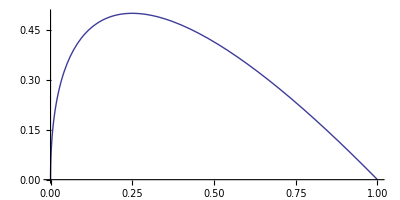

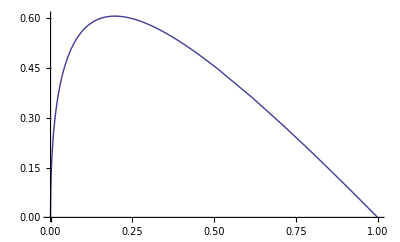

```mathematica
ParametricPlot[{(1-s[t])*(1-s[t+2]),s[t]*(1-s[t+2])+(1-s[t])*s[t+2]},{t,-10,10}]
```

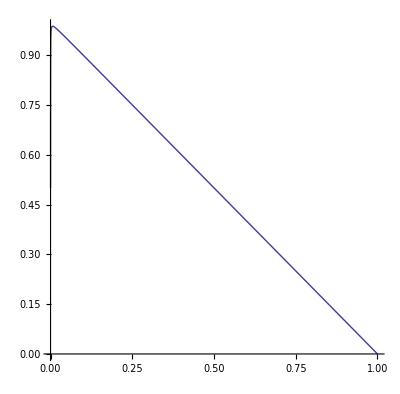

```mathematica
ParametricPlot[{(1-s[t])*(1-s[t-10]),s[t]*(1-s[t-10])+(1-s[t])*s[t-10]},{t,-10,10}]
```